```mathematica
issues = {{1,24},{2,41},{3,90},{4,139},{5,189},{6,243},{7,273},{8,300},{9,309},{10,336},{11,363},{12,414},{13,476},{14,520},{15,542},{16,554},{17,595},{18,665},{19,713},{20,773},{21,834},{22,847},{23,859},{24,927},{25,988},{26,1038},{27,1097},{28,1146},{29,1160},{30,1169},{31,1213},{32,1267},{33,1316},{34,1355},{35,1400},{36,1415},{37,1420},{38,1502},{39,1568},{40,1618},{41,1660},{42,1705},{43,1724},{44,1738},{45,1782},{46,1829},{47,1891},{48,1900}}
```

{{1,24},{2,41},{3,90},{4,139},{5,189},{6,243},{7,273},{8,300},{9,309},{10,336},{11,363},{12,414},{13,476},{14,520},{15,542},{16,554},{17,595},{18,665},{19,713},{20,773},{21,834},{22,847},{23,859},{24,927},{25,988},{26,1038},{27,1097},{28,1146},{29,1160},{30,1169},{31,1213},{32,1267},{33,1316},{34,1355},{35,1400},{36,1415},{37,1420},{38,1502},{39,1568},{40,1618},{41,1660},{42,1705},{43,1724},{44,1738},{45,1782},{46,1829},{47,1891},{48,1900}}

```mathematica
{{1,12},{2,27},{3,32},{4,114},{5,180},{6,230},{7,272},{8,317},{9,336},{10,350},{11,394},{12,400}}
```

Goel-Okumoto model

```mathematica
goel = NonlinearModelFit[issues, a(1 - Exp[-b*t]), {a,b},t]
```

FittedModel[…]

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
goel["BestFit"]
```

30469.7 (1-ⅇ^(-0.00116718 t))

```mathematica
goel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 30469.7 | 822719. | 0.0370354 | 0.971186
b | 0.00116718 | 0.0316877 | 0.0368337 | 0.971343

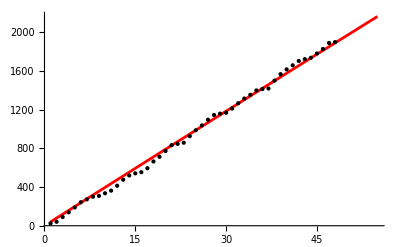

```mathematica
Plot[goel[x], {x, 1, 55}, Epilog->Point[issues], PlotRange->All, PlotStyle->Red]
```

Delayed S-shaped model m(t) = a(1-(1+b*t)Exp[-b*t])

```mathematica
delayedS = NonlinearModelFit[issues,a(1-(1+b*t)Exp[-b*t]),{{a,204}, {b,0.1}},t];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
delayedS["BestFit"]
```

3.22782×10^7 (1-ⅇ^(0.000250557 t) (1-0.000250557 t))

```mathematica
delayedS["ParameterTable"]
```

General::munfl: Exp[-2485.13] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | 3.22782×10^7 | 1.71888×10^-17 | 1.87786×10^24 | 0.
b | -0.000250557 | 4.44383×10^-6 | -56.3832 | 4.15172×10^-44

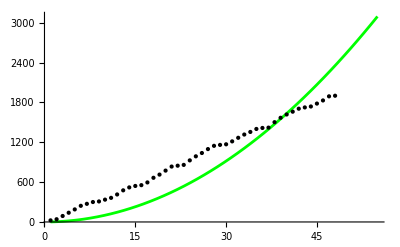

```mathematica
Plot[delayedS[x],{x,1,55},Epilog->Point[issues], PlotRange->All, PlotStyle->Green]
```

Inflection S-shaped model m(t) = a (1-Exp[-b*t]) / 1+ β*Exp[-b*t]

```mathematica
inflection = NonlinearModelFit[issues,(a(1-Exp[-b*t])) / (1+ β*Exp[-b*t]),{{a,204}, {b,0.1},{β}}, t];
```

```mathematica
inflection["BestFit"]
```

(3104.17 (1-ⅇ^(-0.0415778 t)))/(1+3.00997 ⅇ^(-0.0415778 t))

```mathematica
inflection["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 3104.17 | 245.573 | 12.6405 | 2.07679×10^-16
b | 0.0415778 | 0.00450793 | 9.22327 | 6.14831×10^-12
β | 3.00997 | 0.255558 | 11.778 | 2.4246×10^-15

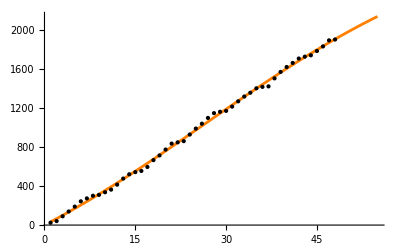

```mathematica
Plot[inflection[x],{x,1,55},Epilog->Point[issues], PlotRange->All, PlotStyle->Orange]
```

Pham-Zhang model

```mathematica
phamZhang=NonlinearModelFit[issues,
(1/(1+β*Exp[-b*t]))*((c+a)*
(1-Exp[-b*t])-((a*b)/(b-α))*(Exp[-α*t]-Exp[-b*t])),{a,b,{c,90},{α,1.1},β},t];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
phamZhang["BestFit"]
```

(5896.5 (1-ⅇ^(-0.0466346 t))-4793.38 (-ⅇ^(-0.0466346 t)+ⅇ^(-0.00624495 t)))/(1+1.57976 ⅇ^(-0.0466346 t))

```mathematica
phamZhang["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 4151.49 | 204582. | 0.0202925 | 0.983904
b | 0.0466346 | 0.151282 | 0.308263 | 0.759371
c | 1745.01 | 7728.31 | 0.225795 | 0.822431
α | 0.00624495 | 0.422419 | 0.0147838 | 0.988273
β | 1.57976 | 18.9706 | 0.0832742 | 0.93402

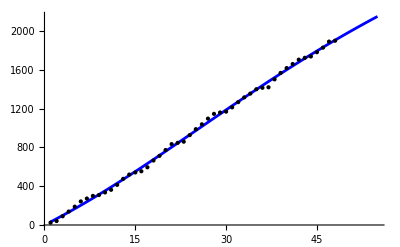

```mathematica
Plot[phamZhang[x],{x,1,55},Epilog->Point[issues], PlotRange->All, PlotStyle->Blue]
```

PHZ model

```mathematica
phz=NonlinearModelFit[issues,
(a/(1+β *Exp[-b*t])) * 
((1-Exp[-b*t])(1-α/b)+α*a*t),
{{a,90},b,α,β},t]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[…]

```mathematica
phz["BestFit"]
```

-(46.1216 (0.999611 (1-ⅇ^(-49.5025 t))-0.887552 t))/(1+87.338 ⅇ^(-49.5025 t))

```mathematica
phz["ParameterTable"]
```

General::munfl: Exp[-742.537] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-792.039] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
a | -46.1216 | 7.73948 | -5.95927 | 3.87327×10^-7
b | 49.5025 | 0.0028021 | 17666.2 | 2.28765×10^-152
α | 0.0192437 | 0.00634617 | 3.03234 | 0.00405883
β | 87.338 | 1.05699×10^-21 | 8.26287×10^22 | 0.

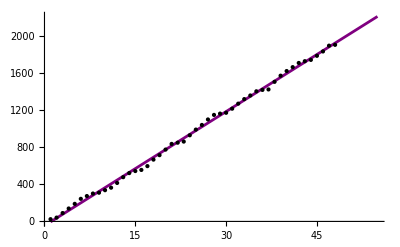

```mathematica
Plot[phz[x],{x,1,55},Epilog->Point[issues], PlotRange->All, PlotStyle->Purple]
```

Rayleigh модел

```mathematica
rayleigh=NonlinearModelFit[issues,a (1-Exp[-b*t^2]),{a,b},t]
```

FittedModel[…]

```mathematica
rayleigh["BestFit"]
```

1907.09 (1-ⅇ^(-0.00119463 t^2))

```mathematica
rayleigh["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 1907.09 | 52.3457 | 36.4326 | 1.41217×10^-35
b | 0.00119463 | 0.0000734166 | 16.2719 | 1.04376×10^-20

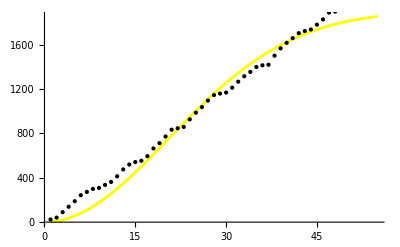

```mathematica
Plot[rayleigh[x],{x,1,55},Epilog->Point[issues],PlotRange->All,PlotStyle->Yellow]
```

Анализ на най-подходящ модел

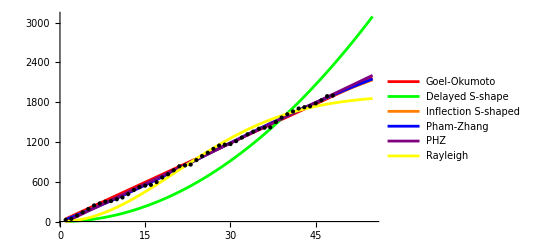

```mathematica
Plot[{goel[x],delayedS[x],inflection[x],phamZhang[x],phz[x],rayleigh[x]},{x,1,55},Epilog->Point[issues],PlotRange->All,PlotStyle->{Red,Green,Orange,Blue,Purple,Yellow},PlotLegends->{"Goel-Okumoto","Delayed S-shape","Inflection S-shaped","Pham-Zhang","PHZ","Rayleigh"}]
```

Оценки със статистически критерии

```mathematica
TableForm[{#,goel[#],delayedS[#],inflection[#],phamZhang[#],phz[#],rayleigh[#]}&/@{"AIC","AICc","BIC","RSquared","AdjustedRSquared"},TableHeadings->{{"AIC","AICc","BIC","RSquared","AdjustedRSquared"},{"Metric","Goel","Delayed S","Inflection S","Pham-Zhang","PHZ","Rayleigh"}}]
```

General::munfl: Exp[-742.537] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-792.039] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Metric | Goel | Delayed S | Inflection S | Pham-Zhang | PHZ | Rayleigh
AIC | AIC | 483.315 | 676.165 | 440.785 | 444.524 | 456.293 | 566.1
AICc | AICc | 483.861 | 676.71 | 441.715 | 446.573 | 457.722 | 566.646
BIC | BIC | 488.929 | 681.779 | 448.27 | 455.752 | 465.649 | 571.714
RSquared | RSquared | 0.999015 | 0.945245 | 0.99961 | 0.999612 | 0.999484 | 0.994472
AdjustedRSquared | AdjustedRSquared | 0.998972 | 0.942865 | 0.999584 | 0.999567 | 0.999437 | 0.994232

Извод: От статистическите критерии се вижда, че Inflection S-shaped има най-нисък AIC (440.785), AICc (441.715), BIC (448.27) и най-висок R.b2 (0.99961) и Adjusted R.b2 (0.999584) 
Следователно Inflection S-shaped е най-добър модел


Предсказание:

```mathematica
prediction = Table[{i,Round[inflection[i]]},{i,49,80}]
```

{{49,1939},{50,1973},{51,2007},{52,2040},{53,2073},{54,2105},{55,2136},{56,2166},{57,2196},{58,2225},{59,2254},{60,2281},{61,2308},{62,2335},{63,2360},{64,2385},{65,2410},{66,2434},{67,2457},{68,2479},{69,2501},{70,2522},{71,2542},{72,2562},{73,2581},{74,2600},{75,2618},{76,2636},{77,2653},{78,2669},{79,2685},{80,2701}}

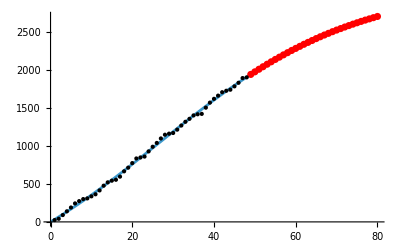

```mathematica
Show[Plot[inflection[x],{x,0,80},Epilog->Point[issues],PlotRange->All],ListPlot[prediction,PlotStyle->Red]]
```